```mathematica
phiBar[deltaPhi_,T_]:=deltaPhi/T;
```

```mathematica
Cp6:=phiBar/(√π(1-3/(2 κ))^(3/2))Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

```mathematica
Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ - 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->κ>3/2&&phiBar>0]
```

((-3+2 κ) ((√((6+4 phiBar-4 κ)/phiBar) (-4+(8 phiBar)/(-3+2 κ))^-κ Gamma[1-κ] Gamma[-1+2 κ])/Gamma[1+κ]+Hypergeometric2F1[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)]/κ))/(2 phiBar)

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ - 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->κ>3/2&&phiBar>0]
```

((-3+2 κ) ((√((6+4 phiBar-4 κ)/phiBar) (-4+(8 phiBar)/(-3+2 κ))^-κ Gamma[1-κ] Gamma[-1+2 κ])/Gamma[1+κ]+Hypergeometric2F1[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)]/κ))/(2 phiBar)

```mathematica
IE2= 1/(RB-1)Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarOverRBm1>0]
```

((-3+2 phiBarOverRBm1+2 κ) (3+(-2+4 phiBarOverRBm1) κ) Hypergeometric2F1[1,1+κ,-1/2,(2 phiBarOverRBm1)/(3-2 κ)]+((3-2 κ)^2-4 phiBarOverRBm1^2 (-1+6 κ+4 κ^2)+phiBarOverRBm1 (-30+8 κ (1+κ))) Hypergeometric2F1[1,1+κ,1/2,(2 phiBarOverRBm1)/(3-2 κ)])/(2 phiBarOverRBm1^2 (-1+RB) (-1+4 κ^2))

```mathematica
IE2/.κ->3
```

1/(70 phiBarOverRBm1^2 (-1+RB))((3+2 phiBarOverRBm1) (3+3 (-2+4 phiBarOverRBm1)) Hypergeometric2F1[1,4,-1/2,-(2 phiBarOverRBm1)/3]+(9+66 phiBarOverRBm1-212 phiBarOverRBm1^2) Hypergeometric2F1[1,4,1/2,-(2 phiBarOverRBm1)/3])

```mathematica
IE1/.κ->3
```

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Indeterminate

### Whoops, this version had the sign of IE2 reversed

```mathematica
FullThing=FullSimplify[Cp6*(IE1-1/(RB-1)IE2)/.phiBarOverRBm1->phiBar/(RB-1)]
```

1/(2 (-3+2 κ)^(3/2))((κ Gamma[κ] (3 (-1+RB) ((-1+RB)^2 (-3+2 κ)^3+2 phiBar (-1+RB) (3-2 κ)^2 (5+2 κ)-4 phiBar^2 (3-20 κ+8 κ^3))-3 (2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))]))/(12 phiBar^2 √(2 π) (-1+RB)^2 Gamma[5/2+κ])+Csc[π κ] (√((3+2 phiBar-2 κ)/phiBar) (-3+2 κ) (-1+(2 phiBar)/(-3+2 κ))^-κ+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]))

```mathematica
(*densFacK[phiBar_,κ_,RB_]:=1/(16 (-3+2 κ)^(3/2))(1/(phiBar^2 (-1+RB) Gamma[5/2+κ])√(2/π) Gamma[1+κ] ((-1+RB) (-3+2 κ) (-(-1+RB)^2 (3-2 κ)^2-2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)+4 phiBar^2 (-1+6 κ+4 κ^2))+(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+8 Csc[π κ] ((3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(1+κ)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]))*)
```

### Here we go

```mathematica
FullThing=FullSimplify[IE1-IE2/.phiBarOverRBm1->phiBar/(RB-1)]
```

1/(16 (-3+2 κ)^(3/2))(-1/(phiBar^2 (-1+RB) Gamma[5/2+κ])√(2/π) Gamma[1+κ] ((-1+RB) (-3+2 κ) (-(-1+RB)^2 (3-2 κ)^2-2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)+4 phiBar^2 (-1+6 κ+4 κ^2))+(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+8 Csc[π κ] ((3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(1+κ)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]))

#### Below is second rearrange

```mathematica
(*densFacK[phiBar_,κ_,RB_]:=1/(16 (-3+2 κ)^(3/2))(-1/(phiBar^2 (RB-1) Gamma[5/2+κ])√(2/π) Gamma[κ+1] ((RB-1) (2 κ-3) (-(RB-1)^2 (2κ - 3)^2-2 phiBar (RB-1) (2 κ-3) (2 κ+5)+4 phiBar^2 (4 κ^2+6 κ-1))+(2 phiBar+(RB-1) (2 κ-3))^3 Hypergeometric2F1[1,κ+1,-1/2,-(2 phiBar)/((RB-1) (2 κ-3))])+8 Csc[κ π] ((3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (2 κ-3)^(1+κ)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,-κ+1,(2 κ-3)/(2 phiBar)])/Gamma[κ-3/2]))*)
```

#### Below is the third rearrange

```mathematica
(*densFacK[phiBar_,κ_,RB_]:=1/(16 (2 κ-3)^(3/2))(-1/(phiBar^2 Gamma[5/2+κ])√(2/π) Gamma[κ+1] (-(RB-1)^2 (2 κ-3)^3-2 phiBar (RB-1) (2 κ-3)^2 (2 κ+5)+4 phiBar^2(2 κ-3) (4 κ^2+6 κ-1)+(RB-1)^2(2κ-3)^3(phiBar/((RB-1)(κ-3/2))+1)^3 Hypergeometric2F1[1,κ+1,-1/2,-(2 phiBar)/((RB-1) (2 κ-3))])+8 Csc[κ π] ((2κ-3)^(3/2)/phiBar^(1/2)(phiBar/(κ-3/2)-1)^(-κ+1/2)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,-κ+1,(2 κ-3)/(2 phiBar)])/Gamma[κ-3/2]))*)
```

#### Below is the fourth rearrange

```mathematica
densFacK[phiBar_,κ_,RB_]:=1/(16 (2 κ-3)^(3/2))(-1/(phiBar^2 Gamma[5/2+κ])√(2/π) Gamma[κ+1] (-2 phiBar (RB-1) (2 κ-3)^2 (2 κ+5)+4 phiBar^2(2 κ-3) (4 κ^2+6 κ-1)+(RB-1)^2(2κ-3)^3((phiBar/((RB-1)(κ-3/2))+1)^3 Hypergeometric2F1[1,κ+1,-1/2,-(2 phiBar)/((RB-1) (2 κ-3))]-1))+8 Csc[κ π] ((2κ-3)^(3/2)/phiBar^(1/2)(phiBar/(κ-3/2)-1)^(-κ+1/2)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,-κ+1,(2 κ-3)/(2 phiBar)])/Gamma[κ-3/2]))
```

#### Below is the fifth rearrange

```mathematica
densFacK[phiBar_,κ_,RB_]:=1/(phiBar^2 Gamma[κ+5/2](2 κ-3)^(3/2))√(1/(2π)) Gamma[κ+1] ( phiBar (RB-1) (κ-3/2)^2 (2 κ+5)-phiBar^2(κ-3/2) (4 κ^2+6 κ-1)+(RB-1)^2(κ-3/2)^3(1-(phiBar/((RB-1)(κ-3/2))+1)^3 Hypergeometric2F1[1,κ+1,-1/2,-(2 phiBar)/((RB-1) (2 κ-3))]))+ Csc[κ π]/2 (1/phiBar^(1/2)(phiBar/(κ-3/2)-1)^(-κ+1/2)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,-κ+1,(2 κ-3)/(2 phiBar)])/((2 κ-3)^(3/2)Gamma[κ-3/2]))
```

### After first rearrange

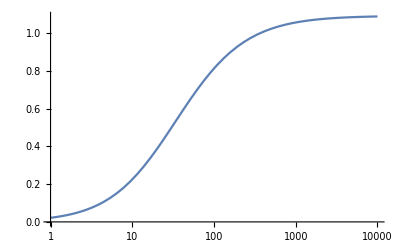

```mathematica
LogLinearPlot[densFacK[941/110,18/10,RB],{RB,1,10000}]
```

### After second rearrange

```mathematica
LogLinearPlot[densFacK[941/110,18/10,RB],{RB,1,10000}]
```

-Graphics-

### After third rearrange

```mathematica
LogLinearPlot[densFacK[941/110,18/10,RB],{RB,1,10000}]
```

-Graphics-

### After fourth rearrange

```mathematica
LogLinearPlot[densFacK[941/110,18/10,RB],{RB,1,10000}]
```

-Graphics-

```mathematica
Manipulate[LogLinearPlot[densFacK[941/110,κ,RB],{RB,1,10000},FrameStyle->(FontSize->17),Epilog->{Text[Style[StringForm["ϕ̄ = `1`, κ = `2`",941/110,κ],15],Scaled[{0.05,0.97}],{-1,1}]},ImageSize->600],{κ,151/100,10}]
```

```mathematica
Limit[densFacK[phiBar,κ,RB],κ->∞]
```

$Aborted